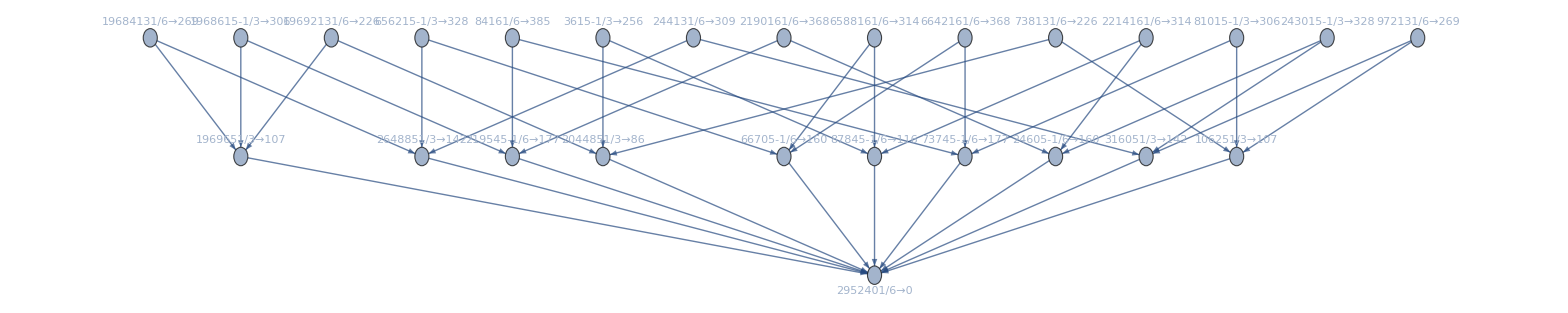
-Graphics-206653→-Graphics-

```mathematica
GenGraph[lambdaKey,"F"]
```

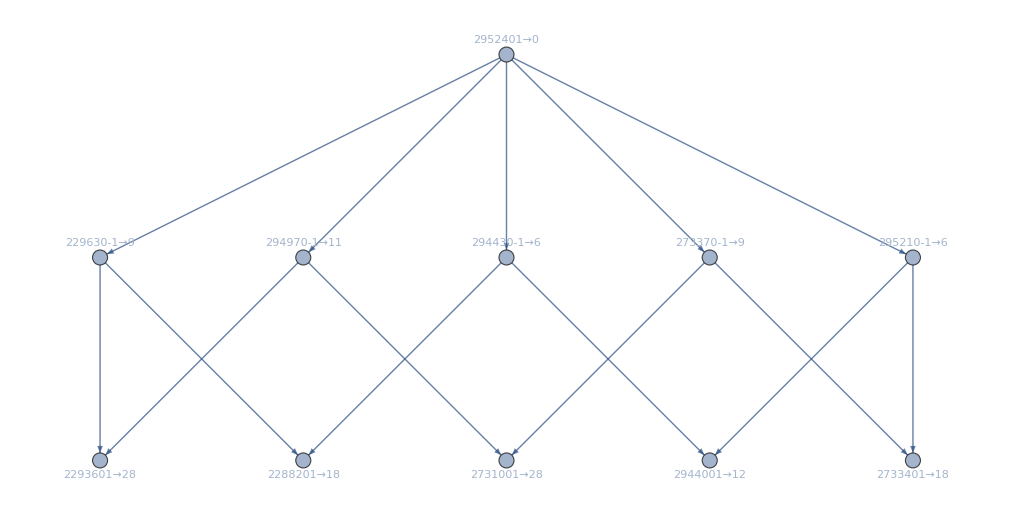
-Graphics-20665363→-Graphics-

```mathematica
GenGraph[lambdaKey,"G"]
```

```mathematica
(28+18+28+12+18)*2/3//N
```

69.3333

```mathematica
(9+11+6+9+6)
```

41

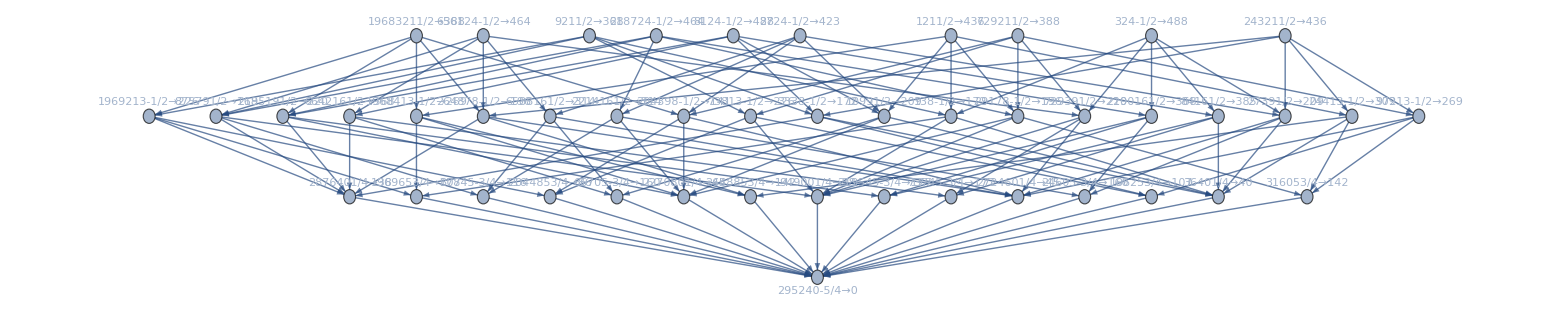

```mathematica
GenGraph[Simplify[Total[Table[allGraphs5[k,"colofournull"],{k,quads}]]],"F"]
```

```mathematica
GenGraph[lambdaKey,"T"]
```

-Graphics-20665363→-Graphics-

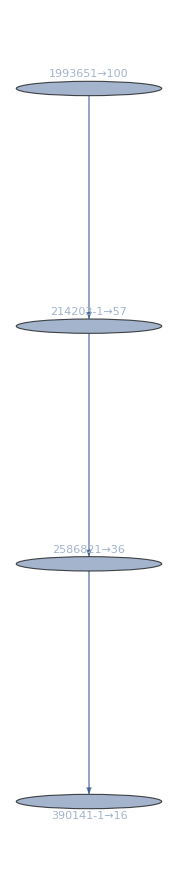

```mathematica
Graph[-Graphics-,ImageSize->{100,500}]
```

```mathematica
FiveNodes=Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&];
```

```mathematica
FiveNodesTrees=Select[FiveNodes,TreeGraphQ[allGraphs5[#,"graph"]]&]
```

{29160,28458,28434,28432,27054,26982,26974,26352,26328,26326,26280,26272,26256,26254,26248,22842,22608,22602,22140,22116,22114,21906,21900,21882,21880,21874,20736,20664,20656,20502,20496,20424,20422,20416,20034,20010,20008,19962,19954,19938,19936,19930,19800,19794,19776,19774,19768,19722,19720,19714,9720,9558,9504,9018,8994,8992,8856,8832,8830,8778,8776,7614,7542,7534,7398,7380,7372,7326,7318,6912,6888,6886,6840,6832,6816,6814,6808,6678,6672,6654,6652,6646,6600,6598,6592,3240,3186,3168,3162,3006,3000,2952,2946,2538,2514,2512,2466,2458,2442,2440,2434,2304,2298,2280,2278,2272,2226,2224,2218,1080,1056,1054,1008,1000,984,982,976,846,840,822,820,814,768,766,760}

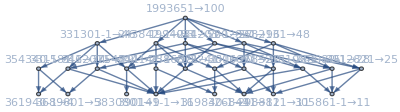
-Graphics-291608167→-Graphics-

```mathematica
GenGraph[29160,"T"]
```

```mathematica
FiveNodesPaths=Select[FiveNodes,PathGraphQ[allGraphs5[#,"graph"]]&]
```

{26328,26329,26326,26280,26281,26272,26254,26248,22116,22117,22114,21906,21909,21900,21882,21874,20664,20665,20656,20502,20505,20496,20424,20422,19936,19930,19776,19768,19722,19720,9018,9019,8992,8856,8859,8832,8778,8776,7614,7615,7534,7398,7407,7380,7372,7326,6886,6832,6678,6672,6646,6598,3240,3243,3186,3195,3168,3162,3000,2952,2514,2466,2458,2434,2298,2226,1056,1054,1008,982,846,822}

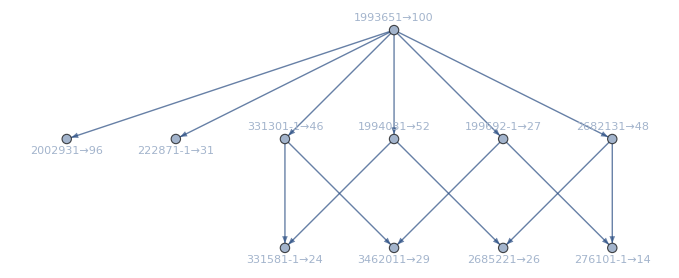
-Graphics-263287209→-Graphics-

```mathematica
GenGraph[26328,"T"]
```

```mathematica
Select[FiveNodesPaths,PathGraphQ[GenGraph[#,"T"][[2]]]&]
```

{20665,19936}

```mathematica
PathGraphQ[allGraphs5[20665,"graph"]]
```

True

```mathematica
GenGraph[20665,"T"]
```

-Graphics-20665363→-Graphics-